Data Import

```mathematica
dataSubj00140=Import["/Users/ivanevtimov/GDrive-Laf/THESIS/Results with more subjects/data_howfar_meb_subject_00140.csv",HeaderLines-> 1];
euclideanFAsSubj00140=dataSubj00140[[All,1]];
euclideanFBsSubj00140=dataSubj00140[[All,2]];
euclideanRCsSubj00140=dataSubj00140[[All,3]];
hammingFAsSubj00140=dataSubj00140[[All,4]];
hammingFBsSubj00140=dataSubj00140[[All,5]];
hammingRCsSubj00140=dataSubj00140[[All,6]];
```

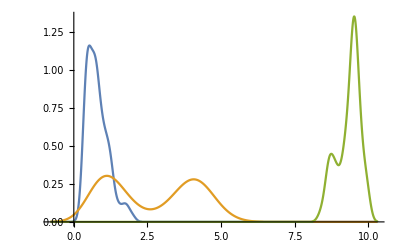

```mathematica
SmoothHistogram[{euclideanFAsSubj00140,euclideanFBsSubj00140,euclideanRCsSubj00140}]
```

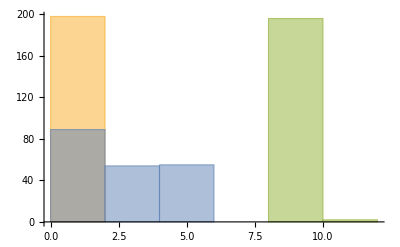

```mathematica
Histogram[{euclideanFAsSubj00140,euclideanFBsSubj00140,euclideanRCsSubj00140}]
```

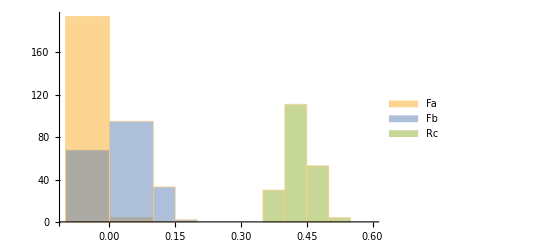

```mathematica
Histogram[{hammingFAsSubj00140,hammingFBsSubj00140,hammingRCsSubj00140},{Join[{-0.1,0.000001},Table[i,{i,0.1,0.6,0.05}]]},ChartLegends->{"Fa","Fb","Rc"}]
```

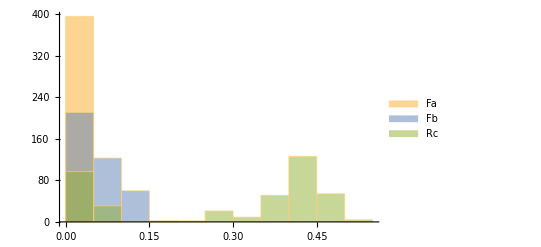

```mathematica
Histogram[{hammingFAsSubj00140,hammingFBsSubj00140,hammingRCsSubj00140},{0.05},ChartLegends->{"Fa","Fb","Rc"}]
```

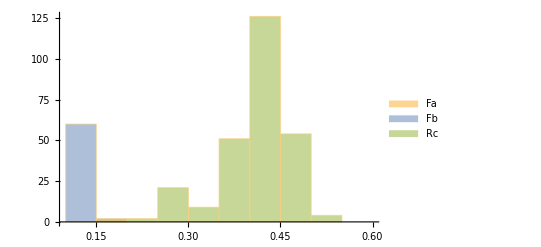

```mathematica
Histogram[{hammingFAsSubj00140,hammingFBsSubj00140,hammingRCsSubj00140},{Table[i,{i,0.1,0.6,0.05}]},ChartLegends->{"Fa","Fb","Rc"}]
```

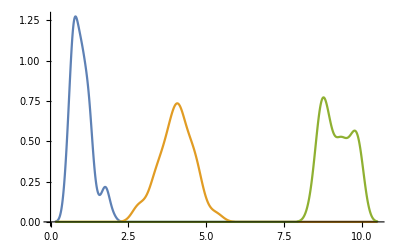

```mathematica
data=Import["/Users/ivanevtimov/GDrive-Laf/THESIS/Results with more subjects/data_howfar_meb_subject_00070.csv",HeaderLines-> 1];
euclideanFAs=data[[All,1]];
euclideanFBs=data[[All,2]];
euclideanRCs=data[[All,3]];
hammingFAs=data[[All,4]];
hammingFBs=data[[All,5]];
hammingRCs=data[[All,6]];
SmoothHistogram[{euclideanFAs,euclideanFBs,euclideanRCs}]
```

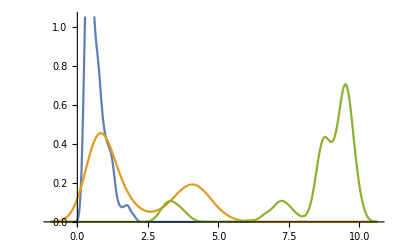

```mathematica
data=Import["/Users/ivanevtimov/GDrive-Laf/THESIS/Results with more subjects/data_howfar_meb_subject_00468.csv",HeaderLines-> 1];
euclideanFAs=data[[All,1]];
euclideanFBs=data[[All,2]];
euclideanRCs=data[[All,3]];
hammingFAs=data[[All,4]];
hammingFBs=data[[All,5]];
hammingRCs=data[[All,6]];
SmoothHistogram[{euclideanFAs,euclideanFBs,euclideanRCs}]
```

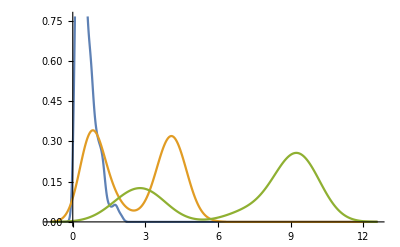

```mathematica
data=Import["/Users/ivanevtimov/GDrive-Laf/THESIS/Results with more subjects/data_howfar_meb_subject_00682.csv",HeaderLines-> 1];
euclideanFAs=data[[All,1]];
euclideanFBs=data[[All,2]];
euclideanRCs=data[[All,3]];
hammingFAs=data[[All,4]];
hammingFBs=data[[All,5]];
hammingRCs=data[[All,6]];
SmoothHistogram[{euclideanFAs,euclideanFBs,euclideanRCs}]
```